## graphSimple – illustration of a simple graph (Section 14.1)

```mathematica
Clear["Global`*"];
```

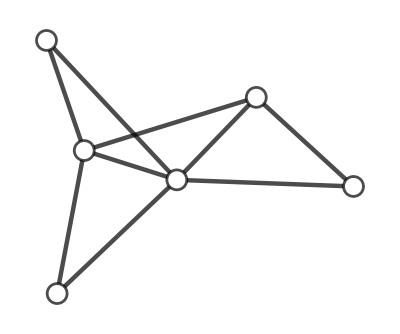

```mathematica
SeedRandom[123];
g0=RandomGraph[BarabasiAlbertGraphDistribution[6,2],VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["graphSimple0.pdf",g0];
*)
```